```mathematica
dataPINN = Import["/Users/jiguangda/Desktop/txu_PINN.csv"][[2;;,;;]];
dataNUMERICAL = Import["/Users/jiguangda/Desktop/txu_NUMERICAL.csv"][[2;;,;;]];
```

```mathematica
ListPlot3D[{dataPINN,dataNUMERICAL},PlotRange->Full, AxesLabel->{"t","x","u"}]
```

-Graphics3D-

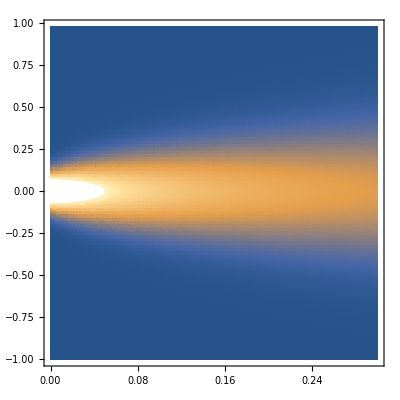

```mathematica
ListDensityPlot[dataPINN]
```

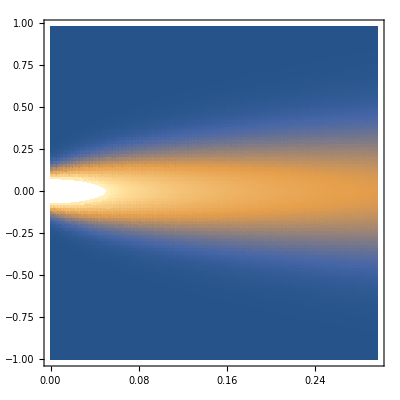

```mathematica
ListDensityPlot[dataNUMERICAL]
```